```mathematica
u0[x_]:=Abs[FractionalPart[Abs[x-1/2]]-1/2]
u[x_, k_]:=u0[x*4^k]/4^k
```

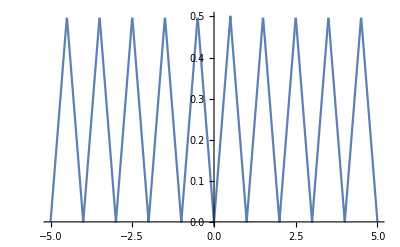

```mathematica
Plot[u[x, 0], {x, -5, 5},AxesStyle->Directive[Black]]
```

3

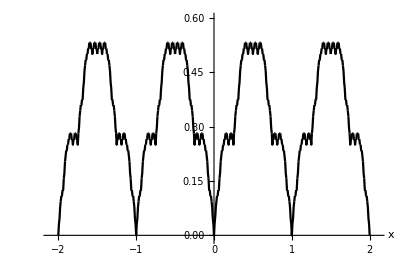

```mathematica
maxK=3
f[x_]:=Sum[u[x, k], {k, 0, maxK}]
p=Plot[f[x], {x, -2, 2},
MaxRecursion-> 15,
AspectRatio->1/1.5,
LabelStyle->(FontFamily->"STIX Two Text"),
PlotStyle->{Black},
AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},
PlotRange-> {{-2.1, 2.1}, {-0.01, 0.6}},
AxesLabel->{x,}]
```

```mathematica
Export["D:\\wolfram\\u_sum.pdf",p]
```

D:\wolfram\u_sum.pdf